# day 23

## code

```mathematica
findAllCliques[g_,{k_}]:=Union@@(Subsets[#,{k}]&/@Select[FindClique[g,Infinity,All],k<=Length[#]&])
```

https://mathematica.stackexchange.com/questions/75245/is-there-a-bug-in-findclique

## part 1

### example

```mathematica
text=Import["/Users/brenton/development/github/AdventOfCode2024/day23/example.txt","Text"];
```

```mathematica
network=StringSplit[#,"-"]&/@StringSplit[text,"\n"]
```

{{kh,tc},{qp,kh},{de,cg},{ka,co},{yn,aq},{qp,ub},{cg,tb},{vc,aq},{tb,ka},{wh,tc},{yn,cg},{kh,ub},{ta,co},{de,co},{tc,td},{tb,wq},{wh,td},{ta,ka},{td,qp},{aq,cg},{wq,ub},{ub,vc},{de,ta},{wq,aq},{wq,vc},{wh,yn},{ka,de},{kh,ta},{co,tc},{wh,qp},{tb,vc},{td,yn}}

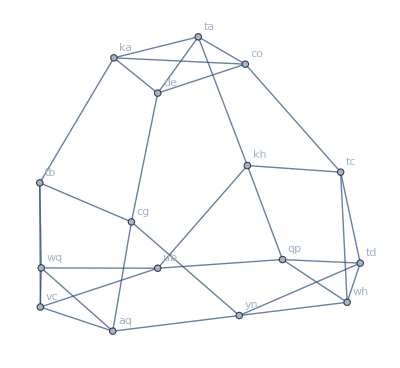

```mathematica
g=Graph[UndirectedEdge@@@network,VertexLabels->"Name"]
```

```mathematica
findAllCliques[g_,{k_}]:=Union@@(Subsets[#,{k}]&/@Select[FindClique[g,Infinity,All],k<=Length[#]&])
```

```mathematica
cliques=findAllCliques[g,{3}]
```

{{aq,vc,wq},{cg,yn,aq},{de,co,ta},{de,ka,co},{de,ka,ta},{ka,co,ta},{kh,qp,ub},{qp,wh,td},{tb,vc,wq},{tc,wh,td},{ub,vc,wq},{yn,wh,td}}

```mathematica
Select[cliques,StringStartsQ[#[[1]],"t"]||StringStartsQ[#[[2]],"t"]||StringStartsQ[#[[3]],"t"]&]
```

{{de,co,ta},{de,ka,ta},{ka,co,ta},{qp,wh,td},{tb,vc,wq},{tc,wh,td},{yn,wh,td}}

### input

```mathematica
text=Import["/Users/brenton/development/github/AdventOfCode2024/day23/input.txt","Text"];
```

```mathematica
network=StringSplit[#,"-"]&/@StringSplit[text,"\n"]
```

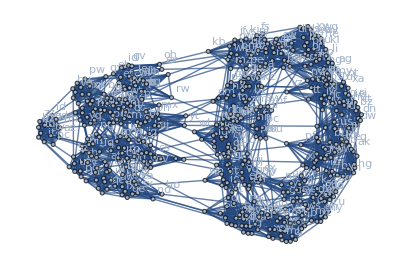

```mathematica
g=Graph[UndirectedEdge@@@network,VertexLabels->"Name"]
```

```mathematica
cliques=findAllCliques[g,{3}]
```

```mathematica
Select[cliques,StringStartsQ[#[[1]],"t"]||StringStartsQ[#[[2]],"t"]||StringStartsQ[#[[3]],"t"]&]
```

{{at,bl,tj},{at,fv,tj},{at,gl,tj},{at,im,tj},{at,lu,tj},{at,mf,tj},{at,nr,tj},{at,sx,tj},{at,tj,oi},{at,vy,tj},{az,ed,td},{az,ed,ty},{az,hz,td},{az,hz,ty},{az,it,td},{az,it,ty},{az,nh,td},{az,nh,ty},{az,pc,td},{az,pc,ty},{az,td,ty},{az,td,ux},{az,td,wc},{az,ty,ux},{az,ty,wc},{az,yg,td},{az,yg,ty},{az,zz,td},{az,zz,ty},{be,bw,tb},{be,tb,ij},{be,tb,jm},{be,tb,qw},{be,tb,rl},{be,tb,wh},{be,tb,zf},{bl,mf,tj},{bl,nr,tj},{bl,tj,oi},{bn,ls,ts},{bn,mx,ts},{bn,ts,gp},{bn,ts,ha},{bn,ts,iv},{bn,ts,jz},{bn,ts,sh},{bn,ts,wx},{bv,cq,ta},{bv,iu,ta},{bv,mg,ta},{bv,oo,ta},{bv,rb,ta},{bv,sm,ta},{bv,ta,hh},{bv,ta,xd},{bv,ta,zi},{bw,tb,ij},{bw,tb,jm},{bw,tb,qw},{bw,tb,rl},{bw,tb,wh},{bw,tb,zf},{ci,ej,ti},{ci,jv,ti},{ci,ry,ti},{ci,ti,jj},{ci,ti,nw},{ci,ti,pr},{ci,ti,va},{ci,ti,xj},{ci,ti,yz},{ck,tm,dm},{ck,tm,es},{ck,tm,gx},{ck,tm,ho},{ck,tm,nx},{ck,tm,vo},{ck,tm,wr},{ck,tm,xn},{cl,tw,fp},{cl,tw,mj},{cl,tw,sb},{cq,iu,ta},{cq,mg,ta},{cq,oo,ta},{cq,sm,ta},{cq,ta,hh},{cq,ta,xd},{cq,ta,zi},{dc,ci,ti},{dc,ej,ti},{dc,jv,ti},{dc,ry,ti},{dc,ti,jj},{dc,ti,nw},{dc,ti,pr},{dc,ti,va},{dc,ti,xj},{dc,ti,yz},{dd,qp,tk},{dd,tk,jc},{dd,tk,kd},{dd,tk,nf},{dh,is,tp},{dh,ja,tp},{dh,jg,tp},{dh,kx,tp},{dh,tp,fz},{dh,tp,ib},{dh,tp,ko},{dh,tp,mb},{dh,tp,mu},{dh,tp,qd},{dh,um,tp},{dr,bv,ta},{dr,cq,ta},{dr,iu,ta},{dr,mg,ta},{dr,oo,ta},{dr,rb,ta},{dr,sm,ta},{dr,ta,hh},{dr,ta,xd},{dr,ta,zi},{dt,cl,tw},{dt,tw,fp},{dt,tw,mj},{dt,tw,sb},{ed,hz,td},{ed,hz,ty},{ed,it,td},{ed,it,ty},{ed,td,ty},{ed,td,ux},{ed,td,wc},{ed,ty,ux},{ed,ty,wc},{ej,ti,jj},{ej,ti,nw},{ej,ti,pr},{ej,ti,va},{ej,ti,xj},{ej,ti,yz},{ew,be,tb},{ew,bw,tb},{ew,sw,tb},{ew,tb,ij},{ew,tb,jm},{ew,tb,qw},{ew,tb,rl},{ew,tb,wh},{ew,tb,zf},{fj,cl,tw},{fj,dt,tw},{fj,rj,tw},{fj,ro,tw},{fj,tw,fp},{fj,tw,mj},{fj,tw,sb},{fj,ui,tw},{fj,zh,tw},{fu,ie,tt},{fu,tt,bs},{fu,tt,gc},{fu,tt,mr},{fu,tt,nm},{fu,tt,ot},{fu,tt,qy},{fu,tt,vi},{fu,tt,xa},{fu,ul,tt},{fu,yu,tt},{fv,bl,tj},{fv,gl,tj},{fv,lu,tj},{fv,mf,tj},{fv,nr,tj},{fv,tj,oi},{fv,vy,tj},{ge,tn,bt},{ge,tn,ep},{ge,tn,hc},{ge,tn,hf},{ge,tn,ju},{ge,tn,ka},{ge,tn,kc},{ge,tn,pm},{ge,tn,ra},{ge,tn,rv},{ge,tn,xh},{gl,bl,tj},{gl,mf,tj},{gl,nr,tj},{gl,tj,oi},{gr,cl,tw},{gr,dt,tw},{gr,fj,tw},{gr,rj,tw},{gr,ro,tw},{gr,tw,fp},{gr,tw,mj},{gr,tw,sb},{gr,ui,tw},{gr,zh,tw},{hb,dd,tk},{hb,qp,tk},{hb,tk,dg},{hb,tk,jc},{hb,tk,kd},{hb,tk,nf},{hb,ws,tk},{hb,yo,tk},{hz,td,ty},{hz,td,ux},{hz,td,wc},{hz,ty,ux},{hz,ty,wc},{ie,tt,bs},{ie,tt,gc},{ie,tt,mr},{ie,tt,ot},{ie,tt,qy},{ie,tt,vi},{ie,tt,xa},{ie,ul,tt},{ie,yu,tt},{im,bl,tj},{im,fv,tj},{im,gl,tj},{im,lu,tj},{im,mf,tj},{im,nr,tj},{im,sx,tj},{im,tj,oi},{im,vy,tj},{is,jg,tp},{is,tp,fz},{is,tp,ib},{is,tp,ko},{is,tp,mb},{is,tp,mu},{is,tp,qd},{is,um,tp},{it,hz,td},{it,hz,ty},{it,td,ty},{it,td,ux},{it,td,wc},{it,ty,ux},{it,ty,wc},{iu,ta,hh},{iu,ta,xd},{iu,ta,zi},{ja,is,tp},{ja,jg,tp},{ja,kx,tp},{ja,tp,ib},{ja,tp,ko},{ja,tp,mb},{ja,tp,mu},{ja,tp,qd},{ja,um,tp},{jg,tp,fz},{jg,tp,ib},{jg,tp,ko},{jg,tp,mb},{jg,tp,mu},{jg,tp,qd},{jg,um,tp},{jv,ej,ti},{jv,ry,ti},{jv,ti,jj},{jv,ti,nw},{jv,ti,pr},{jv,ti,va},{jv,ti,xj},{jv,ti,yz},{kx,is,tp},{kx,jg,tp},{kx,tp,fz},{kx,tp,ib},{kx,tp,ko},{kx,tp,mb},{kx,tp,mu},{kx,tp,qd},{kx,um,tp},{ld,az,td},{ld,az,ty},{ld,ed,td},{ld,ed,ty},{ld,hz,td},{ld,hz,ty},{ld,it,td},{ld,it,ty},{ld,nh,td},{ld,nh,ty},{ld,pc,td},{ld,pc,ty},{ld,td,ty},{ld,td,ux},{ld,td,wc},{ld,ty,ux},{ld,ty,wc},{ld,yg,td},{ld,yg,ty},{ld,zz,td},{ld,zz,ty},{ls,mx,ts},{ls,ts,gp},{ls,ts,ha},{ls,ts,iv},{ls,ts,jz},{ls,ts,sh},{ls,ts,wx},{lu,bl,tj},{lu,gl,tj},{lu,mf,tj},{lu,nr,tj},{lu,tj,oi},{lu,vy,tj},{mf,nr,tj},{mf,tj,oi},{mg,iu,ta},{mg,ta,hh},{mg,ta,xd},{mg,ta,zi},{mt,dd,tk},{mt,hb,tk},{mt,qp,tk},{mt,tk,dg},{mt,tk,jc},{mt,tk,kd},{mt,tk,nf},{mt,vr,tk},{mt,ws,tk},{mt,yo,tk},{mt,zj,tk},{mx,ts,gp},{mx,ts,ha},{mx,ts,iv},{mx,ts,jz},{mx,ts,sh},{mx,ts,wx},{nh,ed,td},{nh,ed,ty},{nh,hz,td},{nh,hz,ty},{nh,it,td},{nh,it,ty},{nh,pc,td},{nh,pc,ty},{nh,td,ty},{nh,td,ux},{nh,td,wc},{nh,ty,ux},{nh,ty,wc},{nh,yg,td},{nh,yg,ty},{nh,zz,td},{nh,zz,ty},{nr,tj,oi},{nv,be,tb},{nv,bw,tb},{nv,ew,tb},{nv,sw,tb},{nv,tb,ij},{nv,tb,jm},{nv,tb,qw},{nv,tb,rl},{nv,tb,wh},{nv,tb,zf},{oo,iu,ta},{oo,mg,ta},{oo,sm,ta},{oo,ta,hh},{oo,ta,xd},{oo,ta,zi},{pc,ed,td},{pc,ed,ty},{pc,hz,td},{pc,hz,ty},{pc,it,td},{pc,it,ty},{pc,td,ty},{pc,td,ux},{pc,td,wc},{pc,ty,ux},{pc,ty,wc},{pc,zz,td},{pc,zz,ty},{pt,bv,ta},{pt,cq,ta},{pt,dr,ta},{pt,iu,ta},{pt,mg,ta},{pt,oo,ta},{pt,rb,ta},{pt,sm,ta},{pt,ta,hh},{pt,ta,xd},{pt,ta,zi},{pz,ck,tm},{pz,tm,dm},{pz,tm,es},{pz,tm,gx},{pz,tm,ho},{pz,tm,nx},{pz,tm,vo},{pz,tm,wr},{pz,tm,xn},{pz,to,ck},{pz,to,dm},{pz,to,es},{pz,to,gx},{pz,to,ho},{pz,to,nx},{pz,to,tm},{pz,to,vb},{pz,to,vo},{pz,to,wr},{pz,to,xn},{qc,at,tj},{qc,bl,tj},{qc,fv,tj},{qc,gl,tj},{qc,im,tj},{qc,lu,tj},{qc,mf,tj},{qc,nr,tj},{qc,sx,tj},{qc,tj,oi},{qc,vy,tj},{qp,tk,dg},{qp,tk,jc},{qp,tk,kd},{qp,tk,nf},{rb,cq,ta},{rb,iu,ta},{rb,mg,ta},{rb,oo,ta},{rb,sm,ta},{rb,ta,hh},{rb,ta,xd},{rj,cl,tw},{rj,dt,tw},{rj,tw,fp},{rj,tw,mj},{rj,tw,sb},{rj,ui,tw},{rj,zh,tw},{ro,cl,tw},{ro,dt,tw},{ro,rj,tw},{ro,tw,mj},{ro,tw,sb},{ro,ui,tw},{ro,zh,tw},{ry,ej,ti},{ry,ti,jj},{ry,ti,nw},{ry,ti,pr},{ry,ti,va},{ry,ti,xj},{ry,ti,yz},{sj,bn,ts},{sj,ls,ts},{sj,mx,ts},{sj,ts,gp},{sj,ts,ha},{sj,ts,iv},{sj,ts,jz},{sj,ts,sh},{sj,ts,wx},{sj,uj,ts},{sm,iu,ta},{sm,mg,ta},{sm,ta,hh},{sm,ta,xd},{sm,ta,zi},{sw,be,tb},{sw,bw,tb},{sw,tb,ij},{sw,tb,jm},{sw,tb,qw},{sw,tb,rl},{sw,tb,wh},{sw,tb,zf},{sx,bl,tj},{sx,fv,tj},{sx,gl,tj},{sx,mf,tj},{sx,nr,tj},{sx,tj,oi},{sx,vy,tj},{ta,xd,hh},{ta,zi,hh},{ta,zi,xd},{tb,ij,jm},{tb,ij,rl},{tb,qw,ij},{tb,qw,jm},{tb,qw,rl},{tb,qw,wh},{tb,qw,zf},{tb,rl,jm},{tb,wh,ij},{tb,wh,jm},{tb,wh,rl},{tb,zf,ij},{tb,zf,jm},{tb,zf,rl},{tb,zf,wh},{td,ty,ux},{td,ty,wc},{td,ux,wc},{ti,nw,jj},{ti,nw,pr},{ti,nw,xj},{ti,pr,jj},{ti,va,jj},{ti,va,nw},{ti,va,pr},{ti,va,xj},{ti,va,yz},{ti,xj,jj},{ti,xj,pr},{ti,yz,jj},{ti,yz,nw},{ti,yz,pr},{ti,yz,xj},{tk,dg,kd},{tk,dg,nf},{tk,jc,dg},{tk,jc,kd},{tk,jc,nf},{tk,nf,kd},{tl,dp,fn},{tl,dp,gs},{tl,fn,gs},{tl,gj,dp},{tl,gj,fn},{tl,gj,gs},{tl,gj,mo},{tl,gj,mq},{tl,gj,so},{tl,gj,su},{tl,gj,sv},{tl,gj,ug},{tl,gj,xf},{tl,gj,yk},{tl,mo,dp},{tl,mo,fn},{tl,mo,gs},{tl,mo,mq},{tl,mo,so},{tl,mo,sv},{tl,mq,dp},{tl,mq,fn},{tl,mq,gs},{tl,mq,so},{tl,so,dp},{tl,so,fn},{tl,so,gs},{tl,su,dp},{tl,su,fn},{tl,su,gs},{tl,su,mo},{tl,su,mq},{tl,su,so},{tl,su,sv},{tl,sv,dp},{tl,sv,fn},{tl,sv,gs},{tl,sv,mq},{tl,sv,so},{tl,ug,dp},{tl,ug,fn},{tl,ug,gs},{tl,ug,mo},{tl,ug,mq},{tl,ug,so},{tl,ug,su},{tl,ug,sv},{tl,xf,dp},{tl,xf,fn},{tl,xf,gs},{tl,xf,mo},{tl,xf,mq},{tl,xf,so},{tl,xf,su},{tl,xf,sv},{tl,xf,ug},{tl,yk,dp},{tl,yk,fn},{tl,yk,mo},{tl,yk,mq},{tl,yk,so},{tl,yk,su},{tl,yk,sv},{tl,yk,ug},{tl,yk,xf},{tm,dm,es},{tm,dm,gx},{tm,dm,ho},{tm,dm,nx},{tm,dm,wr},{tm,dm,xn},{tm,es,ho},{tm,gx,es},{tm,gx,ho},{tm,gx,xn},{tm,nx,es},{tm,nx,gx},{tm,nx,ho},{tm,nx,wr},{tm,nx,xn},{tm,vo,dm},{tm,vo,es},{tm,vo,gx},{tm,vo,ho},{tm,vo,nx},{tm,vo,wr},{tm,vo,xn},{tm,wr,es},{tm,wr,gx},{tm,wr,ho},{tm,wr,xn},{tm,xn,es},{tm,xn,ho},{tn,bt,hc},{tn,bt,hf},{tn,bt,ju},{tn,bt,ka},{tn,bt,kc},{tn,bt,pm},{tn,bt,ra},{tn,bt,xh},{tn,ep,bt},{tn,ep,hc},{tn,ep,hf},{tn,ep,ju},{tn,ep,ka},{tn,ep,kc},{tn,ep,pm},{tn,ep,ra},{tn,ep,xh},{tn,hc,ju},{tn,hc,ka},{tn,hc,xh},{tn,hf,hc},{tn,hf,ju},{tn,hf,ka},{tn,hf,xh},{tn,ju,ka},{tn,kc,hc},{tn,kc,hf},{tn,kc,ju},{tn,kc,ka},{tn,kc,xh},{tn,pm,hc},{tn,pm,hf},{tn,pm,ju},{tn,pm,ka},{tn,pm,kc},{tn,pm,ra},{tn,pm,xh},{tn,ra,hc},{tn,ra,hf},{tn,ra,ju},{tn,ra,ka},{tn,ra,kc},{tn,rv,bt},{tn,rv,ep},{tn,rv,hc},{tn,rv,hf},{tn,rv,ju},{tn,rv,ka},{tn,rv,kc},{tn,rv,pm},{tn,rv,ra},{tn,rv,xh},{tn,xh,ju},{tn,xh,ka},{to,ck,dm},{to,ck,es},{to,ck,gx},{to,ck,ho},{to,ck,nx},{to,ck,tm},{to,ck,vb},{to,ck,vo},{to,ck,wr},{to,ck,xn},{to,dm,es},{to,dm,gx},{to,dm,ho},{to,dm,nx},{to,dm,vb},{to,dm,wr},{to,dm,xn},{to,es,ho},{to,gx,es},{to,gx,ho},{to,gx,vb},{to,gx,xn},{to,nx,es},{to,nx,gx},{to,nx,ho},{to,nx,vb},{to,nx,wr},{to,nx,xn},{to,tm,dm},{to,tm,es},{to,tm,gx},{to,tm,ho},{to,tm,nx},{to,tm,vo},{to,tm,wr},{to,tm,xn},{to,vb,es},{to,vb,ho},{to,vb,xn},{to,vo,dm},{to,vo,es},{to,vo,gx},{to,vo,ho},{to,vo,nx},{to,vo,vb},{to,vo,wr},{to,vo,xn},{to,wr,es},{to,wr,gx},{to,wr,ho},{to,wr,vb},{to,wr,xn},{to,xn,es},{to,xn,ho},{tp,fz,ko},{tp,fz,mu},{tp,ib,fz},{tp,ib,ko},{tp,ib,mb},{tp,ib,mu},{tp,ib,qd},{tp,ko,mu},{tp,mb,fz},{tp,mb,ko},{tp,mb,mu},{tp,mb,qd},{tp,qd,fz},{tp,qd,ko},{tp,qd,mu},{ts,gp,jz},{ts,gp,wx},{ts,ha,gp},{ts,ha,jz},{ts,ha,wx},{ts,iv,gp},{ts,iv,ha},{ts,iv,jz},{ts,iv,wx},{ts,jz,wx},{ts,sh,gp},{ts,sh,ha},{ts,sh,iv},{ts,sh,jz},{ts,sh,wx},{tt,bs,gc},{tt,bs,mr},{tt,bs,nm},{tt,bs,vi},{tt,gc,mr},{tt,gc,nm},{tt,gc,vi},{tt,mr,nm},{tt,ot,bs},{tt,ot,gc},{tt,ot,mr},{tt,ot,nm},{tt,ot,qy},{tt,ot,vi},{tt,ot,xa},{tt,qy,bs},{tt,qy,gc},{tt,qy,mr},{tt,qy,nm},{tt,qy,vi},{tt,vi,mr},{tt,vi,nm},{tt,xa,bs},{tt,xa,gc},{tt,xa,mr},{tt,xa,nm},{tt,xa,qy},{tt,xa,vi},{tw,fp,mj},{tw,fp,sb},{tw,mj,sb},{ty,ux,wc},{ui,cl,tw},{ui,dt,tw},{ui,tw,fp},{ui,tw,mj},{ui,tw,sb},{ui,zh,tw},{uj,bn,ts},{uj,ls,ts},{uj,mx,ts},{uj,ts,gp},{uj,ts,ha},{uj,ts,iv},{uj,ts,jz},{uj,ts,sh},{uj,ts,wx},{uj,yt,ts},{ul,tt,bs},{ul,tt,gc},{ul,tt,mr},{ul,tt,nm},{ul,tt,ot},{ul,tt,qy},{ul,tt,vi},{ul,tt,xa},{um,tp,fz},{um,tp,ib},{um,tp,ko},{um,tp,mb},{um,tp,mu},{um,tp,qd},{vr,dd,tk},{vr,hb,tk},{vr,qp,tk},{vr,tk,dg},{vr,tk,jc},{vr,tk,kd},{vr,tk,nf},{vr,ws,tk},{vr,yo,tk},{vr,zj,tk},{vy,bl,tj},{vy,gl,tj},{vy,mf,tj},{vy,nr,tj},{vy,tj,oi},{ws,dd,tk},{ws,qp,tk},{ws,tk,dg},{ws,tk,jc},{ws,tk,kd},{ws,tk,nf},{ws,yo,tk},{xl,cl,tw},{xl,dt,tw},{xl,fj,tw},{xl,gr,tw},{xl,rj,tw},{xl,ro,tw},{xl,tw,fp},{xl,tw,mj},{xl,tw,sb},{xl,ui,tw},{xl,zh,tw},{yg,ed,td},{yg,ed,ty},{yg,hz,td},{yg,hz,ty},{yg,it,td},{yg,it,ty},{yg,pc,td},{yg,pc,ty},{yg,td,ty},{yg,td,ux},{yg,td,wc},{yg,ty,ux},{yg,ty,wc},{yg,zz,td},{yg,zz,ty},{yo,dd,tk},{yo,qp,tk},{yo,tk,dg},{yo,tk,jc},{yo,tk,kd},{yo,tk,nf},{yt,bn,ts},{yt,ls,ts},{yt,mx,ts},{yt,ts,gp},{yt,ts,ha},{yt,ts,iv},{yt,ts,jz},{yt,ts,sh},{yt,ts,wx},{yu,tt,bs},{yu,tt,gc},{yu,tt,mr},{yu,tt,nm},{yu,tt,ot},{yu,tt,qy},{yu,tt,vi},{yu,tt,xa},{yu,ul,tt},{zh,cl,tw},{zh,dt,tw},{zh,tw,fp},{zh,tw,mj},{zh,tw,sb},{zj,dd,tk},{zj,hb,tk},{zj,qp,tk},{zj,tk,dg},{zj,tk,jc},{zj,tk,kd},{zj,tk,nf},{zj,ws,tk},{zj,yo,tk},{zz,ed,td},{zz,ed,ty},{zz,hz,td},{zz,hz,ty},{zz,it,td},{zz,it,ty},{zz,td,ty},{zz,td,ux},{zz,td,wc},{zz,ty,ux},{zz,ty,wc}}

```mathematica
%//Length
```

926

## part 2

```mathematica
StringJoin[Riffle[Sort[FindClique[g][[1]]],","]]
```

az,ed,hz,it,ld,nh,pc,td,ty,ux,wc,yg,zz